# Insert Update

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx;
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/"];
p = 0;
μ = Import["DiagMC_BEC.json", {"Data", "Chemical_Potential"} ];
α = Import["DiagMC_BEC.json", {"Data", "Alpha"} ];
mr = Import["DiagMC_BEC.json", {"Data", "Impurity_Mass"} ];
qc = 200;
taus = Import["data/zero_order", "table"][[All,1]];
FP = Import["DiagMC_BEC.json", {"Data", "Froehlich_Polaron"} ];
```

```mathematica
f[q_,τ_]:= vq2[q]*g0[q,0,τ]*dq[q,0,τ]/g0[0,0,τ];
```

```mathematica
NSolve[f[q,1] == 0.5, q, Reals]
```

{{q→-1.17279},{q→-0.00490892},{q→0.00490892},{q→1.17279}}

```mathematica
f[q_,τ_]:= vq2[q]*g0[q,0,τ]*dq[q,0,τ]/g0[0,0,τ];
f[1000,0.1]
```

5.5144387100165×10^-147403

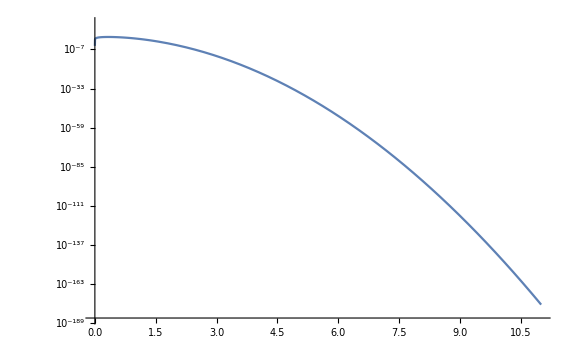

```mathematica
LogPlot[f[q, 1], {q,0,11}]
```

```mathematica
Plot3D[f[q,t], {q, 0, qc}, {t, 0, 1}]
```

-Graphics3D-

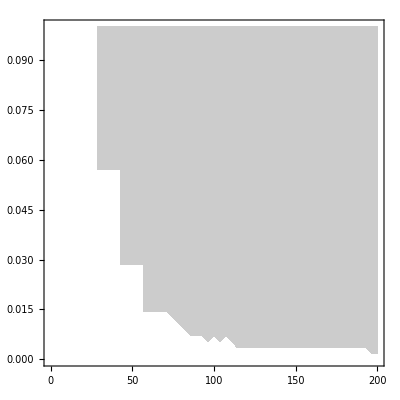

```mathematica
ContourPlot[f[q,t], {q, 0, qc}, {t, 0, 0.1} ]
```